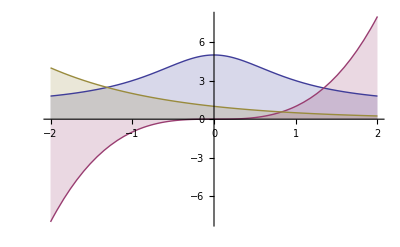

6.5911

```mathematica
f1[x_] := 1 + 4/(x^2+1)
f2[x_]:= x^3
f3[x_] := 2^(-x)
Plot[{f1[x], f2[x], f3[x]}, {x, -2, 2}, Filling -> Axis]
Integrate[f1[x]-f2[x], {x, 0.825, 1.343}] + Integrate[f1[x]-f3[x], {x, -1.307, 0.825}]
```